```mathematica
BeginPackage["Optimise`SimplexOptimise`"];
```

```mathematica
SimplexOptimise::usage="SimplexOptimise[Dimension of Problem, Ranges, Scale Factor, Iterations, Objective Function]";
```

```mathematica
SimplexOptimise2::usage="SimplexOptimise2[Dimension of Problem, Ranges, Scale Factor, Iterations, Objective Function]";
```

```mathematica
SimplexOptimise3::usage="SimplexOptimise3[Dimension of Problem, Ranges, Iterations, Objective Function]";
```

```mathematica
SimplexOptimise3b::usage="SimplexOptimise3[Dimension of Problem, Ranges, Iterations, Objective Function]";
```

```mathematica
SimplexOptimise4::usage="SimplexOptimise4[Dimension of Problem, Ranges, Scale Factor, Iterations, Objective Function]; Same as SimplexOptimise3, but with NO output.";
```

```mathematica
SimplexFinish::usage="SimplexFinish[]\nStops the current simplex and writes the output"
```

```mathematica
Begin["`Private`"]
```

SimplexOptimise`Private`

```mathematica
CreateSimplex[no_,range_?(Length[Dimensions[#1]]===1&),factor_,opts___]:=Block[{a,start,b},start=Global`StartSimplex/.{opts}/.{Global`StartSimplex->0};If[ListQ[start],a=start,a=RandomReal[range,no]];b=(ReplacePart[a,RandomReal[{range⟦1⟧,range⟦2⟧}],#1]&)/@Range[no];Flatten[{{a},b},1]]
```

```mathematica
CreateSimplex[no_,range_?(Length[Dimensions[#1]]>1&),factor_,opts___]:=Block[{a,start,b},start=Global`StartSimplex/.{opts}/.{Global`StartSimplex->0};If[ListQ[start],a=Flatten[start],If[Length[range]<no,a=(RandomReal[#1]&)/@PadRight[range,no,{range⟦-1⟧}];,a=(RandomReal[#1]&)/@range]];b=(ReplacePart[a,RandomReal[{range⟦#1,1⟧,range⟦#1,2⟧}],#1]&)/@Range[1,no,1];Flatten[{{a},b},1]]
```

```mathematica
CreateNewSimplex[no_,factor_,a_,opts___]:=Block[{},b=(ReplacePart[a,RandomReal[{1/factor,factor}],#1]&)/@Range[1,no,1];Flatten[{{a},b},1]]
```

```mathematica
Clear[ReflectSimplex]
```

```mathematica
ReflectSimplex[list_,pos_,λin_:1,range_]:=Block[{a,b,c,new,λ=λin},a=Drop[list,{pos}];b=Mean/@Transpose[a];While[!And@@MapThread[#1>#2⟦1⟧&&#1<#2⟦2⟧&,{c=b-λ (list⟦pos⟧-b),range}],λ=λ RandomReal[{0.1,0.9}]];ReplacePart[list,c,pos]]
```

```mathematica
Clear[SimplexOptimise]
```

```mathematica
ReflectSimplex3[list_,pos_,λin_:1,range_]:=Block[{a,b,c,new,λ=λin},
a=Drop[list,{pos}];
b=Map[Mean,Transpose[a]];
c=b-λ(list⟦pos⟧-b);
ReplacePart[list,pos->c]]
```

#### SimplexOptimise1

```mathematica
SimplexOptimise[no_,range_,factor_,iterations_,fitval_,opts___]:=Block[{λ,notimes,list1,ans1,list2,data,ans2,pos,alldataold=Table[∞,{no+1}]},converge=Converge/.{opts}/.{Converge->0};subtimes=SubTimes/.{opts}/.{SubTimes->3};λ=factor;list1=CreateSimplex[no,range,factor,opts];Print[list1];rawdata2={list1};alldata=(fitval[#1]&)/@list1;ans1=alldata;Do[pos=Flatten[Position[ans1,Max[ans1]]]⟦RandomInteger[{1,Length[Flatten[Position[ans1,Max[ans1]]]]}]⟧;list2=ReflectSimplex[list1,pos,λ,range];data=fitval[list2⟦pos⟧];ans2=ReplacePart[ans1,data,pos];notimes=0;While[ans1⟦pos⟧≤ans2⟦pos⟧&&notimes<subtimes,notimes+=1;λ=RandomReal[{1/factor,factor}];list2=ReflectSimplex[list1,pos,λ,range];data=fitval[list2⟦pos⟧];ans2=ReplacePart[ans1,data,pos];];λ=1;ans1=ans2;list1=list2;alldata=ReplacePart[alldata,data,pos];AppendTo[rawdata2,list1];If[alldata⟦-1⟧<Min[Most[alldata]]||ι===1,Print[alldata⟦-1⟧]];If[Abs[Min[alldata]-Min[alldataold]]<converge,Print["Converged!"];Break[]];alldataold=alldata;,{ι,1,iterations}];{Min[alldata],rawdata2⟦-1,First[Position[alldata,Min[alldata]]⟦All,1⟧]⟧}]
```

```mathematica
SimplexOptimise[no_,range_,factor_,iterations_,fitval_,opts___]/;(Maximise/.{opts})===True:=Block[{λ,notimes,list1,ans1,list2,data,ans2,pos,alldataold=Table[-∞,{no+1}]},Print["Maximising!"];converge=Converge/.{opts}/.{Converge->∞};λ=factor;list1=CreateSimplex[no,range,factor,opts];Print[list1];rawdata2={list1};alldata=(fitval[#1]&)/@list1;ans1=alldata;Do[pos=Flatten[Position[ans1,Min[ans1]]]⟦RandomInteger[{1,Length[Flatten[Position[ans1,Min[ans1]]]]}]⟧;list2=ReflectSimplex[list1,pos,λ,range];data=fitval[list2⟦pos⟧];ans2=ReplacePart[ans1,data,pos];notimes=0;While[ans1⟦pos⟧>ans2⟦pos⟧&&notimes<10,notimes+=1;λ=RandomReal[{1/factor,factor}];list2=ReflectSimplex[list1,pos,λ,range];data=fitval[list2⟦pos⟧];ans2=ReplacePart[ans1,data,pos];];λ=1;ans1=ans2;list1=list2;alldata=ReplacePart[alldata,data,pos];AppendTo[rawdata2,list1];If[Max[alldata]>Max[alldataold]||ι===1,Print[Max[alldata]]];If[Max[alldata]≥converge,Print["Converged!"];Break[]];alldataold=alldata;{rawdata2⟦-1,First[Position[alldata,Max[alldata]]⟦All,1⟧]⟧},{ι,1,iterations}];{Max[alldata],rawdata2⟦-1,First[Position[alldata,Max[alldata]]⟦All,1⟧]⟧}]
```

#### SimplexOptimise2

```mathematica
SimplexOptimise2[no_,range_,factor2_,iterations_,FitnessValue_,bigit_Integer,opts___]:=Block[{λ,notimes,list1,list3,list2,list4,data,data1,data2,data3,data4,ans1,ans2,rawdata2,good2,factor,j},factor=factor2;Do[(λ=1;If[j===1,list1=CreateSimplex[no,range,factor,opts],list1=CreateNewSimplex[no,factor,good2]];rawdata2={list1};alldata=(FitnessValue[#1]&)/@list1;If[j===1,good2=list1⟦1⟧];ans1=alldata;Do[pos=Flatten[Position[ans1,Max[ans1]]]⟦RandomInteger[{1,Length[Flatten[Position[ans1,Max[ans1]]]]}]⟧;list2=ReflectSimplex[list1,pos,1];data=FitnessValue[list2⟦pos⟧];If[data<Max[ans1]&&data≥Min[ans1],ans2=ReplacePart[ans1,data,pos];list1=list2;alldata=ReplacePart[alldata,data,pos]];If[data<Min[ans1],list3=ReflectSimplex[list1,pos,factor=RandomReal[{1,factor}]];data3=FitnessValue[list3⟦pos⟧];If[data3<data,ans2=ReplacePart[ans1,data3,pos];list1=list3;alldata=ReplacePart[alldata,data3,pos],ans2=ReplacePart[ans1,data,pos];list1=list2;alldata=ReplacePart[alldata,data,pos]]];If[data>Max[ans1],list4=ReflectSimplex[list1,pos,factor=factor RandomReal[{0,1}]];data4=FitnessValue[list4⟦pos⟧];If[data4≤Max[ans1],ans2=ReplacePart[ans1,data4,pos];list1=list4;alldata=ReplacePart[alldata,data4,pos],notimes=0;While[data4>Max[ans1]&&notimes<3,notimes+=1;list4=ReflectSimplex[list1,pos,RandomReal[{0,factor}]];data4=FitnessValue[list4⟦pos⟧];ans2=ReplacePart[ans1,data4,pos]];list1=list4;alldata=ReplacePart[alldata,data4,pos]]];ans1=ans2;AppendTo[rawdata2,list1];,{ι,1,Ceiling[iterations/bigit]}];Print[Min[alldata]]);If[Min[alldata]<FitnessValue[good2],good2=Last[rawdata2]⟦Position[alldata,Min[alldata]]⟦1,1⟧⟧;factor=factor/2,factor=factor 1.5;];,{j,1,bigit}];good2]
```

#### Analysis

```mathematica
Ca=N[√(1/2 (3-√5))]
```

0.618034

```mathematica
points={{0,0,0},{1,0,2},{1,-1,-1}};
```

```mathematica
pointsr=ReflectSimplex3[points,3,-1,{}]
```

{{0,0,0},{1,0,2},{1,-1,-1}}

```mathematica
λ=1;flipped=False;
λdata={};
While[Abs[λ]≤1,
AppendTo[λdata,
Graphics3D[Line[Join[#,#⟦{1}⟧]]&[ReflectSimplex3[points,3,λ,{}]]]];
If[λ<10^-1||flipped===True,flipped=True;λ=-RandomReal[{Abs[λ]/Ca,Abs[λ]}],λ=RandomReal[{λ Ca,λ}]];
];Show@λdata
```

-Graphics3D-

```mathematica
λ=1;
flipped=False;
λdata={};
While[Abs[λ]≤1.01,
If[λ<10^-3||flipped===True,flipped=True;λ=-Abs[λ]/Ca,λ=λ Ca];
AppendTo[λdata,λ];
]
```

```mathematica
λdata
```

{0.618034,0.381966,0.236068,0.145898,0.0901699,0.0557281,0.0344419,0.0212862,0.0131556,0.00813062,0.005025,0.00310562,0.00191938,0.00118624,0.000733137,-0.00118624,-0.00191938,-0.00310562,-0.005025,-0.00813062,-0.0131556,-0.0212862,-0.0344419,-0.0557281,-0.0901699,-0.145898,-0.236068,-0.381966,-0.618034,-1.,-1.61803}

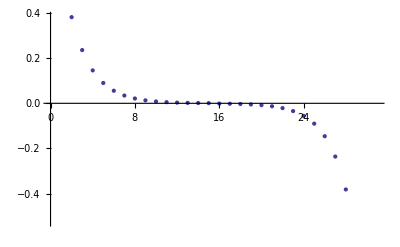

```mathematica
ListPlot[λdata]
```

```mathematica
SimplexFinish[]:=SIMPLEXCONTINUE=False;
```

#### SimplexOptimise3

```mathematica
RandomSeed
```

```mathematica
Less[11,10]
```

False

```mathematica
LessEqual
```

```mathematica
SimplexOptimise3[no_,range_,iterations_,fitval_,opts___]:=Block[{subtimes,startall,less,lessequal,min,max,greater,ordering,expansionfactor,compressionfactor,startingfactor,start,verbose,randomseed,dowhile,fitevaluate,retries,parallel},
NOTIMES=0;
SIMPLEXCONTINUE=True;
subtimes=Global`SubTimes/.{opts}/.{Global`SubTimes->5};
startall=Global`StartAll/.{opts}/.{Global`StartAll->{}};
If[Global`Maximise/.{opts}/.{Global`Maximise->False},
less=Greater;
lessequal=GreaterEqual;
min=Max;
max=Min;
greater=Less;
ordering=Reverse@Ordering[#]&;
,
less=Less;
lessequal=LessEqual;
min=Min;
max=Max;
greater=Greater;
ordering=Ordering;
];
expansionfactor=Global`ExpansionFactor/.{opts}/.{Global`ExpansionFactor->(1&)};
If[Head[expansionfactor]=!=Function,expansionfactor=(Evaluate[expansionfactor]&)];
compressionfactor=Global`CompressionFactor/.{opts}/.{Global`CompressionFactor->(1&)};
If[Head[compressionfactor]=!=Function,compressionfactor=(Evaluate[compressionfactor]&)];
startingfactor=Global`StartingFactor/.{opts}/.{Global`StartingFactor->0.5};
fitevaluate:=Global`StepEvaluate/.{opts}/.{Global`StepEvaluate->""};
start=Start/.{opts}/.{Start->{}};

verbose=Verbose/.{opts}/.{Verbose->True};

randomseed=Global`InputSeed/.{opts}/.{Global`InputSeed->0};

parallel=Global`Parallel/.{opts}/.{Global`Parallel->False};

retries=Global`Retries/.{opts}/.{Global`Retries->True};
If[retries===False,Print["No Retries!"]];
Module[{ι=0,j=0,mindata,minvalue=∞,expfactor,comfactor,converge,convergence,λe,λc,λ,ans1,pos,list2,data,ans2,tempdata,templist,flipped,list1,alldataold,C=N[√(1/2 (3-√5))],poss},
dowhile:=Global`DoWhile/.{opts}/.{Global`DoWhile->j<1};
If[verbose,Print[Dynamic[ι],"  ",Dynamic[minvalue],"   ",Dynamic[mindata],"\tLast Worst Value = ",Dynamic[Last[alldata]⟦Last[ordering[Last[alldata]]]⟧],"\tExpansion/Compression = ",Dynamic[expfactor],"/",Dynamic[comfactor],"\tConverge = ",Dynamic[converge]];
Print[Dynamic[Refresh[fitevaluate,TrackedSymbols->{minvalue}],None]];
];

While[(dowhile/.{Global`NumberIterations->iterations,Global`Best->minvalue,Global`Restarts->j})&&SIMPLEXCONTINUE,
j++;
(*Print[randomseed];*)
If[j===1&&randomseed=!=0,SeedRandom[randomseed],SeedRandom[]];
ι=0;minvalue=∞;
converge:=Abs[Global`Converge/.{opts}/.{Global`Converge->0}/.{Global`NumberIterations->iterations,Global`Best->minvalue,Global`Restarts->j}];
convergence:=Global`Convergence/.{opts}/.{Global`Convergence->If[Global`Maximise,∞,0]}/.{Global`NumberIterations->iterations,Global`Best->minvalue,Global`Restarts->j};

If[startall=!={},
list1=startall];
If[start=!={},list1=CreateSimplex[no,range,1,Global`StartSimplex->start,opts]];
If[j>1,list1=CreateSimplex[no,range,1,Global`StartSimplex->mindata,opts],list1=CreateSimplex[no,range,1,opts]];

rawdata2={list1};
alldata={(fitval[#1]&)/@list1};
ans1=alldata⟦1⟧;
Catch[While[ι≤iterations&&SIMPLEXCONTINUE,
ι++;
λ=startingfactor;
λe=1/(1-C^2) (expfactor=expansionfactor[ι]/.{Global`NumberIterations->iterations,Global`Best->minvalue,Global`Restarts->j});
λc=C^2/(comfactor=compressionfactor[ι]/.{Global`NumberIterations->iterations,Global`Best->minvalue,Global`Restarts->j});
pos=Flatten[Position[ans1,Max[ans1]]]⟦RandomInteger[{1,Length[Flatten[Position[ans1,Max[ans1]]]]}]⟧;
list2=ReflectSimplex3[list1,pos,λ,range];
data=fitval[list2⟦pos⟧];
NOTIMES++;flipped=False;
ans2=ReplacePart[ans1,data,pos];
tempdata=data;
templist=list2;
poss=-1;
pos=ordering[ans1]⟦poss⟧;
If[lessequal[ans1⟦pos⟧,data] ,
While[lessequal[ans1⟦pos⟧,data],
If[Less[λ,10^-startingfactor]||flipped===True,flipped=True;λ=-Abs[λ]/λc,λ=λc λ];
If[LessEqual[λ,-startingfactor]&&Length[ans1]>Abs[poss],λ=startingfactor;flipped=False;poss--;pos=ordering[ans1]⟦poss⟧;,If[Length[ans1]===Abs[poss],If[verbose,Print["run out"]];Throw[Null]]];
list2=ReflectSimplex3[list1,pos,λ,range];
data=fitval[list2⟦pos⟧];
NOTIMES++;
templist=list2;
tempdata=data;
];,
If[retries,
tempdata=Max[ans1];
While[greater[tempdata,data],
tempdata=data;
templist=list2;
λ=λe λ;
list2=ReflectSimplex3[list1,pos,λ,range];
data=fitval[list2⟦pos⟧];
NOTIMES+=1;
]
]
];
ans2=ReplacePart[ans1,tempdata,pos];
ans1=ans2;
list1=templist;
alldata={Sequence@@alldata,ans1};
AppendTo[rawdata2,list1];
If[less[min[alldata⟦-1⟧],min[alldataold]]||ι===1,
minvalue=min[alldata⟦-1⟧];mindata=rawdata2⟦-1,(Position[#1,min[#1]]⟦1,1⟧&)[alldata⟦-1⟧]⟧;
];
If[Abs[Min[alldata⟦-1⟧]-Max[alldata⟦-1⟧]]<Abs@(converge/.{Global`NumberIterations->iterations,Global`Best->minvalue,Global`Restarts->j}),If[verbose,Print["Converge"]];Throw[Null]];
If[less[min[alldata⟦-1⟧],(convergence/.{Global`NumberIterations->iterations,Global`Best->minvalue,Global`Restarts->j})],If[verbose,Print["Convergence"]];Throw[Null]];
alldataold=alldata⟦-1⟧;
]
]
];
FinishDynamic[];
If[verbose,
Print["Minimum Fitness: ",min[alldata⟦-1⟧],"\tRaw Value: ",rawdata2⟦-1,First[Position[alldata⟦-1⟧,min[alldata⟦-1⟧]]⟦All,1⟧]⟧,"\tTotal No. Iterations: ",NOTIMES,"\tNumber Restarts = ",j]];
{min[alldata⟦-1⟧],rawdata2⟦-1,First[Position[alldata⟦-1⟧,min[alldata⟦-1⟧]]⟦All,1⟧]⟧}
]
]
```

#### SimplexOptimise3b

```mathematica
SimplexOptimise3b[no_,range_,iterations_,fitval_,opts___]:=Block[{λ,notimes=0,list1,ans1,list2,data,ans2,pos,alldataold=Table[∞,{no+1}],C=N[√(1/2 (3-√5))],tempdata,templist,flipped,j=0,poss},
subtimes=Global`SubTimes/.{opts}/.{Global`SubTimes->5};
startall=Global`StartAll/.{opts}/.{Global`StartAll->{}};
expansionfactor=Global`ExpansionFactor/.{opts}/.{Global`ExpansionFactor->(1&)};
If[Head[expansionfactor]=!=Function,expansionfactor=(Evaluate[expansionfactor]&)];
fitevaluate:=Global`StepEvaluate/.{opts}/.{Global`StepEvaluate->""};
start=Start/.{opts}/.{Start->{}};
λ=expansionfactor[1]/.{Global`NumberIterations->iterations};

dowhile:=Global`DoWhile/.{opts}/.{Global`DoWhile->j<1};
DynamicModule[{ι=0,mindata,minvalue=∞,expfactor,converge},
converge:=Abs[Global`Converge/.{opts}/.{Global`Converge->0}/.{Global`NumberIterations->iterations,Global`Best->minvalue,Global`Restarts->j}];
Print[Dynamic[ι],"  ",Dynamic[minvalue],"   ",Dynamic[mindata],"\tLast Worst Value = ",Dynamic[Max[Last[alldata]]],"\tExpansion = ",Dynamic[expfactor],"\tConverge = ",Dynamic[converge]];
Print[Dynamic[Refresh[fitevaluate,TrackedSymbols->{minvalue}]]];
While[dowhile/.{Global`NumberIterations->iterations,Global`Best->minvalue,Global`Restarts->j},
j++;
ι=0;minvalue=∞;
If[startall=!={}&&j>1,list1=startall,
If[j>1,list1=CreateSimplex[no,range,1,Global`StartSimplex->mindata,opts],list1=CreateSimplex[no,range,1,opts]]];
rawdata2={list1};
alldata={(fitval[#1]&)/@list1};
ans1=alldata⟦1⟧;
Catch[While[ι≤iterations,ι++;
λ=expfactor=expansionfactor[ι]/.{Global`NumberIterations->iterations};
pos=Flatten[Position[ans1,Max[ans1]]]⟦RandomInteger[{1,Length[Flatten[Position[ans1,Max[ans1]]]]}]⟧;
list2=ReflectSimplex3[list1,pos,λ,range];
data=fitval[list2⟦pos⟧];
notimes+=1;flipped=False;
ans2=ReplacePart[ans1,data,pos];
tempdata=data;
templist=list2;
poss=-1;
pos=Ordering[ans1]⟦poss⟧;
If[ans1⟦pos⟧≤data ,
While[ans1⟦pos⟧≤tempdata,
If[λ≤-expfactor&&Length[ans1]>Abs[poss],λ=expfactor;flipped=False;poss--;pos=Ordering[ans1]⟦poss⟧;,If[Length[ans1]≤Abs[poss],Print["Converged!"];Throw[Null]]];
list2=ReflectSimplex3[list1,pos,λ,range];
data=fitval[list2⟦pos⟧];

notimes+=1;
templist=list2;
tempdata=data;
If[λ<10^-1||flipped===True,flipped=True;λ=-Abs[λ]/C,λ=λ C];
];,
tempdata=Max[ans1];
While[tempdata>data,
tempdata=data;
templist=list2;
notimes+=1;
λ=λ/(1-C);
list2=ReflectSimplex3[list1,pos,λ,range];
data=fitval[list2⟦pos⟧];
notimes+=1;
]
];
ans2=ReplacePart[ans1,tempdata,pos];
ans1=ans2;
list1=templist;
alldata={Sequence@@alldata,ans1};
AppendTo[rawdata2,list1];
If[Min[alldata⟦-1⟧]<Min[alldataold]||ι===1,
minvalue=Min[alldata⟦-1⟧];mindata=rawdata2⟦-1,(Position[#1,Min[#1]]⟦1,1⟧&)[alldata⟦-1⟧]⟧;
];
If[Abs[Min[alldata⟦-1⟧]-Max[alldata⟦-1⟧]]<Abs@(converge/.{Global`NumberIterations->iterations,Global`Best->minvalue,Global`Restarts->j}),Throw[Null]];
alldataold=alldata⟦-1⟧;
]
]
];
FinishDynamic[];
];
Print["Minimum Fitness: ",Min[alldata⟦-1⟧],"\tRaw Value: ",rawdata2⟦-1,First[Position[alldata⟦-1⟧,Min[alldata⟦-1⟧]]⟦All,1⟧]⟧,"\tTotal No. Iterations: ",notimes];
{Min[alldata⟦-1⟧],rawdata2⟦-1,First[Position[alldata⟦-1⟧,Min[alldata⟦-1⟧]]⟦All,1⟧]⟧}
]
```

#### SimplexOptimise4

```mathematica
SimplexOptimise4[no_,range_,iterations_,fitval_,opts___]:=Block[{λ,λe,λc,notimes=0,list1,ans1,list2,data,ans2,pos,alldataold=Table[∞,{no+1}],C=N[√(1/2 (3-√5))],tempdata,templist,flipped,j=0,poss},
SIMPLEXCONTINUE=True;
subtimes=Global`SubTimes/.{opts}/.{Global`SubTimes->5};
startall=Global`StartAll/.{opts}/.{Global`StartAll->{}};

expansionfactor=Global`ExpansionFactor/.{opts}/.{Global`ExpansionFactor->(1&)};
If[Head[expansionfactor]=!=Function,expansionfactor=(Evaluate[expansionfactor]&)];
compressionfactor=Global`CompressionFactor/.{opts}/.{Global`CompressionFactor->(1&)};
If[Head[compressionfactor]=!=Function,compressionfactor=(Evaluate[compressionfactor]&)];

fitevaluate:=Global`StepEvaluate/.{opts}/.{Global`StepEvaluate->""};
start=Start/.{opts}/.{Start->{}};


dowhile:=Global`DoWhile/.{opts}/.{Global`DoWhile->j<1};
DynamicModule[{ι=0,mindata,minvalue=∞,expfactor,comfactor,converge},
SIMPLEXOUTPUTPANEL=Panel[Grid[{{Dynamic[ι],"  ",Dynamic[minvalue],"   ",Dynamic[mindata],"\tLast Worst Value = ",Dynamic[Last[alldata]⟦Last[Ordering[Last[alldata]]]⟧],"\tExpansion/Compression = ",Dynamic[expfactor],"/",Dynamic[comfactor],"\tConverge = ",Dynamic[converge]},{Dynamic[Refresh[fitevaluate,TrackedSymbols->{minvalue}],None]}}]];
While[(dowhile/.{Global`NumberIterations->iterations,Global`Best->minvalue,Global`Restarts->j})&&SIMPLEXCONTINUE,
j++;
ι=0;minvalue=∞;
converge:=Abs[Global`Converge/.{opts}/.{Global`Converge->0}/.{Global`NumberIterations->iterations,Global`Best->minvalue,Global`Restarts->j}];
If[startall=!={}&&j>1,list1=startall,
If[j>1,list1=CreateSimplex[no,range,1,Global`StartSimplex->mindata,opts],list1=CreateSimplex[no,range,1,opts]]];
rawdata2={list1};
alldata={(fitval[#1]&)/@list1};
ans1=alldata⟦1⟧;
Catch[While[ι≤iterations&&SIMPLEXCONTINUE,
ι++;
λ=1;
λe=1/(1-C) (expfactor=expansionfactor[ι]/.{Global`NumberIterations->iterations,Global`Best->minvalue,Global`Restarts->j});
λc=C/(comfactor=compressionfactor[ι]/.{Global`NumberIterations->iterations,Global`Best->minvalue,Global`Restarts->j});
pos=Flatten[Position[ans1,Max[ans1]]]⟦RandomInteger[{1,Length[Flatten[Position[ans1,Max[ans1]]]]}]⟧;
list2=ReflectSimplex3[list1,pos,λ,range];
data=fitval[list2⟦pos⟧];
notimes+=1;flipped=False;
ans2=ReplacePart[ans1,data,pos];
tempdata=data;
templist=list2;
poss=-1;
pos=Ordering[ans1]⟦poss⟧;
If[ans1⟦pos⟧≤data ,
While[ans1⟦pos⟧≤data,
If[λ<10^-1||flipped===True,flipped=True;λ=-Abs[λ]/λc,λ=λc λ];
If[λ≤-1&&Length[ans1]>Abs[poss],λ=1;flipped=False;poss--;pos=Ordering[ans1]⟦poss⟧;,If[Length[ans1]===Abs[poss],Throw[Null]]];
list2=ReflectSimplex3[list1,pos,λ,range];
data=fitval[list2⟦pos⟧];
notimes+=1;
templist=list2;
tempdata=data;
];,
tempdata=Max[ans1];
While[tempdata>data,
tempdata=data;
templist=list2;
λ=λe λ;
list2=ReflectSimplex3[list1,pos,λ,range];
data=fitval[list2⟦pos⟧];
notimes+=1;
]
];
ans2=ReplacePart[ans1,tempdata,pos];
ans1=ans2;
list1=templist;
alldata={Sequence@@alldata,ans1};
AppendTo[rawdata2,list1];
If[Min[alldata⟦-1⟧]<Min[alldataold]||ι===1,
minvalue=Min[alldata⟦-1⟧];mindata=rawdata2⟦-1,(Position[#1,Min[#1]]⟦1,1⟧&)[alldata⟦-1⟧]⟧;
];
If[Abs[Min[alldata⟦-1⟧]-Max[alldata⟦-1⟧]]<Abs@(converge/.{Global`NumberIterations->iterations,Global`Best->minvalue,Global`Restarts->j}),Throw[Null]];
alldataold=alldata⟦-1⟧;
]
]
];
FinishDynamic[];
];
{Min[alldata⟦-1⟧],rawdata2⟦-1,First[Position[alldata⟦-1⟧,Min[alldata⟦-1⟧]]⟦All,1⟧]⟧}
]
```

#### End

```mathematica
End[]
```

SimplexOptimise`Private`

```mathematica
EndPackage[]
```